## Dunaev Viktor, 3 kurs, 6 group , Variant 23

## Task 1

## Create.

## Task 2

```mathematica
fname = NotebookDirectory[]<>"input.txt"
```

C:\6_Cemestr\DS_Lagudo\input.txt

```mathematica
stream = OpenRead[fname];
```

```mathematica
information = ReadList[stream,String]
```

{/*|I|*/ 6,/*|U|*/ 12,{1,5},{2,5},{3,1},{3,4},{3,5},{4,1},{4,2},{4,6},{5,4},{6,2},{6,3},{6,5},/*b_1*/ 7,/*b_2*/ 4,/*b_3*/ -1,/*b_4*/ -7,/*b_5*/ -2,/*b_6*/ -1}

```mathematica
numVertex = Read[StringToStream[StringSplit[information⟦1⟧]⟦2⟧],Number]
```

6

```mathematica
MyVertex = Table[i,{i,1,numVertex}]
```

{1,2,3,4,5,6}

```mathematica
numEdges = Read[StringToStream[StringSplit[information⟦2⟧]⟦2⟧],Number]
```

12

```mathematica
MyEdges = Table[
list = StringSplit[information⟦i⟧,{"{","}",","}];
Read[StringToStream[list⟦1⟧],Number]->Read[StringToStream[list⟦2⟧],Number],
{i,3,2+numEdges}
]
```

{1→5,2→5,3→1,3→4,3→5,4→1,4→2,4→6,5→4,6→2,6→3,6→5}

```mathematica
Close[stream]
```

C:\6_Cemestr\DS_Lagudo\input.txt

## Task 3

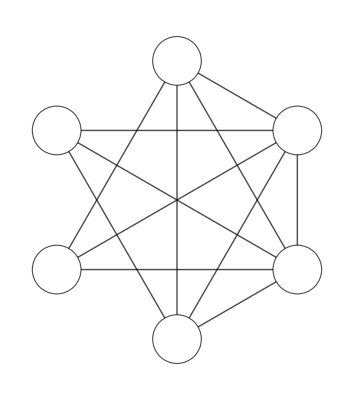

```mathematica
myGraph = Graph[MyVertex,MyEdges,VertexLabels->Placed["Name",Center], GraphLayout->"CircularEmbedding",VertexSize->0.35, VertexStyle->White,EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.035],EdgeStyle->Black,VertexLabelStyle->Large]
```

## Task 4

```mathematica
MyB = Table[
Read[StringToStream[StringSplit[information⟦i⟧]⟦2⟧],Number],
{i,3+numEdges,Length[information]}
]
```

{7,4,-1,-7,-2,-1}

```mathematica
Var = {}
```

{}

```mathematica
MySystem =Table[
eq=0;
For[k=1,k≤Length[MyEdges],k++,
If[MyEdges⟦k⟧⟦1⟧==i,eq=eq+Subscript[Subscript[x, MyEdges⟦k⟧⟦1⟧], MyEdges⟦k⟧⟦2⟧];AppendTo[Var,Subscript[Subscript[x, MyEdges⟦k⟧⟦1⟧], MyEdges⟦k⟧⟦2⟧]]];
If[MyEdges⟦k⟧⟦2⟧==i,eq=eq-Subscript[Subscript[x, MyEdges⟦k⟧⟦1⟧], MyEdges⟦k⟧⟦2⟧];AppendTo[Var,Subscript[Subscript[x, MyEdges⟦k⟧⟦1⟧], MyEdges⟦k⟧⟦2⟧]]];
];
eq==MyB⟦i⟧,
{i,1,numVertex}
]
```

{x_1_5-x_3_1-x_4_1==7,x_2_5-x_4_2-x_6_2==4,x_3_1+x_3_4+x_3_5-x_6_3==-1,-x_3_4+x_4_1+x_4_2+x_4_6-x_5_4==-7,-x_1_5-x_2_5-x_3_5+x_5_4-x_6_5==-2,-x_4_6+x_6_2+x_6_3+x_6_5==-1}

```mathematica
MatrixForm[MySystem]
```

(x_1_5-x_3_1-x_4_1==7
x_2_5-x_4_2-x_6_2==4
x_3_1+x_3_4+x_3_5-x_6_3==-1
-x_3_4+x_4_1+x_4_2+x_4_6-x_5_4==-7
-x_1_5-x_2_5-x_3_5+x_5_4-x_6_5==-2
-x_4_6+x_6_2+x_6_3+x_6_5==-1)

```mathematica
Var1 = Union[Var]
```

{x_1_5,x_2_5,x_3_1,x_3_4,x_3_5,x_4_1,x_4_2,x_4_6,x_5_4,x_6_2,x_6_3,x_6_5}

## Task 5

```mathematica
Solve[MySystem,Var1]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x_4_1→-7+x_1_5-x_3_1,x_5_4→x_1_5-x_3_1-x_3_4+x_4_2+x_4_6,x_6_2→-4+x_2_5-x_4_2,x_6_3→1+x_3_1+x_3_4+x_3_5,x_6_5→2-x_2_5-x_3_1-x_3_4-x_3_5+x_4_2+x_4_6}}

```mathematica
Simplify[%]
```

{{x_4_1→-7+x_1_5-x_3_1,x_5_4→x_1_5-x_3_1-x_3_4+x_4_2+x_4_6,x_6_2→-4+x_2_5-x_4_2,x_6_3→1+x_3_1+x_3_4+x_3_5,x_6_5→2-x_2_5-x_3_1-x_3_4-x_3_5+x_4_2+x_4_6}}